Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{1.62335}

{0.731569}

{0.0294358/(0.731569+0.0228662 i)^3}

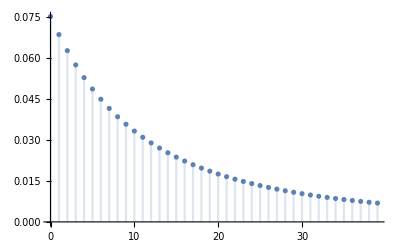

{41.6803}

```mathematica
Clear["`*"]
$Assumptions={Element[ratio,Reals],Element[sigmaMax,Reals],Element[sigmaMin,Reals],Element[a,Reals],ratio>1,sigmaMax>0,sigmaMin>0,sigmaMax>sigmaMin};

ratioValue=ratio->2.219;
ratioRule=sigmaMax->(ratio*sigmaMin);

sigma=sigmaMin+i*(sigmaMax-sigmaMin)/n;
distribution=a/sigma^3/.ratioRule/.ratioValue//FullSimplify;
numSpecies=40;
n=numSpecies-1;

moment0=Sum[distribution,{i,0,n}]/.ratioRule/.ratioValue//FullSimplify;
moment1=Sum[distribution*sigma,{i,0,n}]/.ratioRule/.ratioValue//FullSimplify;
subRule=Solve[{moment0==1,moment1==1},{a,sigmaMin}]/.ratioValue//FullSimplify;

sigmaMax=sigmaMax/.ratioRule/.subRule/.ratioValue//FullSimplify
sigmaMin=sigmaMin/.subRule/.ratioValue//FullSimplify

distributionInsert=distribution/.subRule/.ratioValue//Flatten
DiscretePlot[distributionInsert,{i,0,n}]

totalVolume=Sum[Pi*sigma^3/6,{i,0,numSpecies}]
```